## NMR Relaxation of 1H of water molecules

### Reading the data files obtained from the MD simulations' trajectories:

```mathematica
listRelaxDipInter = Import["Relaxation_dipolar_intermolecular_tip3pCsCl_nvt_500.dat"];
coef00DipInter = Table[{10*listRelaxDipInter[[n+1,1]], listRelaxDipInter[[n+1,2]]},{n,1,Length[listRelaxDipInter]-2} ];
coef11DipInter = Table[{10*listRelaxDipInter[[n+1,1]], listRelaxDipInter[[n+1,3]]},{n,1,Length[listRelaxDipInter]-2} ];
coef22DipInter = Table[{10*listRelaxDipInter[[n+1,1]], listRelaxDipInter[[n+1,5]]},{n,1,Length[listRelaxDipInter]-2} ];

listRelaxDipIntra = Import["Relaxation_dipolar_intramolecular_tip3pCsCl_nvt_all.dat"];
coef00DipIntra = Table[{10*listRelaxDipIntra[[n+1,1]], listRelaxDipIntra[[n+1,2]]},{n,1,Length[listRelaxDipIntra]-2} ];
coef11DipIntra = Table[{10*listRelaxDipIntra[[n+1,1]], listRelaxDipIntra[[n+1,3]]},{n,1,Length[listRelaxDipIntra]-2} ];
coef22DipIntra = Table[{10*listRelaxDipIntra[[n+1,1]], listRelaxDipIntra[[n+1,5]]},{n,1,Length[listRelaxDipIntra]-2} ];
```

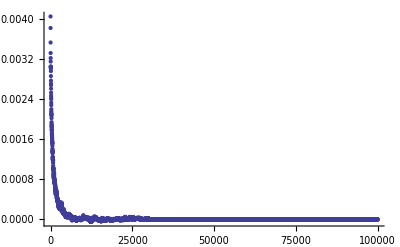

```mathematica
ListPlot[coef00DipInter, PlotRange-> All]
```

### Obtaining interpolating functions and/or fits of the data:

```mathematica
Interpolcoef00DipInter = Interpolation[coef00DipInter];
Interpolcoef11DipInter = Interpolation[coef11DipInter];
Interpolcoef22DipInter = Interpolation[coef22DipInter];

Interpolcoef00DipIntra = Interpolation[coef00DipIntra];
Interpolcoef11DipIntra = Interpolation[coef11DipIntra];
Interpolcoef22DipIntra = Interpolation[coef22DipIntra];
```

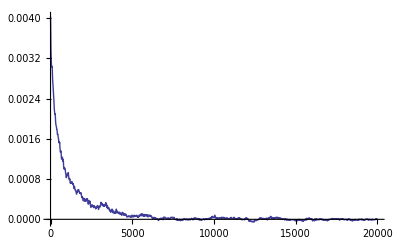

```mathematica
Plot[Interpolcoef00DipInter[x],{x,1, 20000}, PlotRange-> All]
```

#### Intermolecular contribution

{a→0.00299025,b→0.00108288}

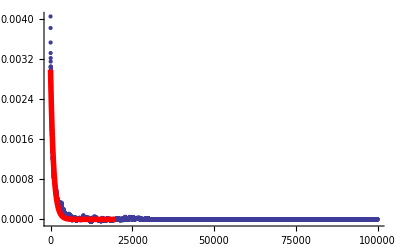

```mathematica
resfit00DipInter = FindFit[coef00DipInter, a*Exp[-b*x],{a,b},x]
a00DipInter = a /. resfit00DipInter[[1]]; b00DipInter = b /. resfit00DipInter[[2]];
Fitcoef00DipInter[x_] = a00DipInter*Exp[-b00DipInter*x];
Show[ListPlot[coef00DipInter, PlotRange-> All],Plot[Fitcoef00DipInter[x],{x,1,20000}, PlotRange-> {0,20000},PlotStyle->{Red, Thickness-> 0.01}]]
```

{a→0.000467084,b→0.000958116}

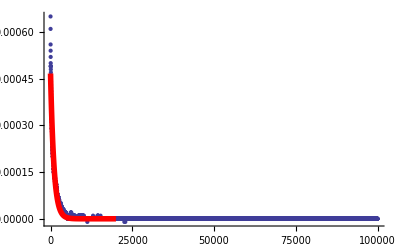

```mathematica
resfit11DipInter = FindFit[coef11DipInter, a*Exp[-b*x],{a,b},x]
a11DipInter = a /. resfit11DipInter[[1]]; b11DipInter = b /. resfit11DipInter[[2]];
Fitcoef11DipInter[x_] = a11DipInter*Exp[-b11DipInter*x];
Show[ListPlot[coef11DipInter, PlotRange-> All],Plot[Fitcoef11DipInter[x],{x,1,20000}, PlotRange-> {0,20000},PlotStyle->{Red, Thickness-> 0.01}]]
```

{a→0.00198898,b→0.00105514}

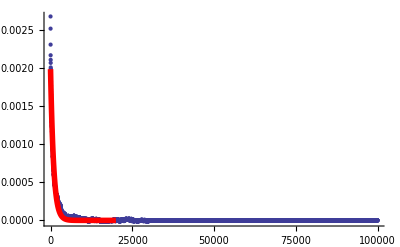

```mathematica
resfit22DipInter = FindFit[coef22DipInter, a*Exp[-b*x],{a,b},x]
a22DipInter = a /. resfit22DipInter[[1]]; b22DipInter = b /. resfit22DipInter[[2]];
Fitcoef22DipInter[x_] = a22DipInter*Exp[-b22DipInter*x];
Show[ListPlot[coef22DipInter, PlotRange-> All],Plot[Fitcoef22DipInter[x],{x,1,20000}, PlotRange-> {0,20000},PlotStyle->{Red, Thickness-> 0.01}]]
```

#### Intramolecular contribution

{a→0.045529,b→0.000942387}

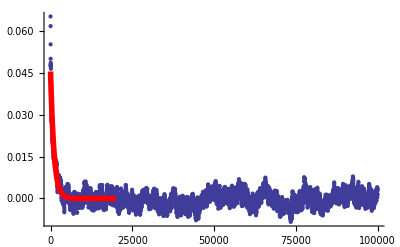

```mathematica
resfit00DipIntra = FindFit[coef00DipIntra, a*Exp[-b*x],{a,b},x]
a00DipIntra = a /. resfit00DipIntra[[1]]; b00DipIntra = b /. resfit00DipIntra[[2]];
Fitcoef00DipIntra[x_] = a00DipIntra*Exp[-b00DipIntra*x];
Show[ListPlot[coef00DipIntra, PlotRange-> All],Plot[Fitcoef00DipIntra[x],{x,1,20000}, PlotRange-> {0,20000},PlotStyle->{Red, Thickness-> 0.01}]]
```

{a→0.00774148,b→0.000870095}

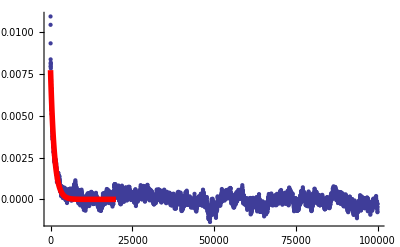

```mathematica
resfit11DipIntra = FindFit[coef11DipIntra, a*Exp[-b*x],{a,b},x]
a11DipIntra = a /. resfit11DipIntra[[1]]; b11DipIntra = b /. resfit11DipIntra[[2]];
Fitcoef11DipIntra[x_] = a11DipIntra*Exp[-b11DipIntra*x];
Show[ListPlot[coef11DipIntra, PlotRange-> All],Plot[Fitcoef11DipIntra[x],{x,1,20000}, PlotRange-> {0,20000},PlotStyle->{Red, Thickness-> 0.01}]]
```

{a→0.0334769,b→0.000940765}

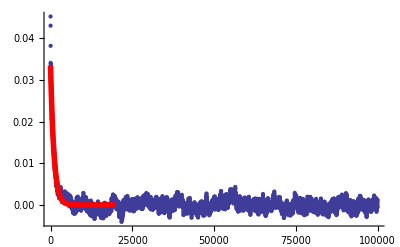

```mathematica
resfit22DipIntra = FindFit[coef22DipIntra, a*Exp[-b*x],{a,b},x]
a22DipIntra = a /. resfit22DipIntra[[1]]; b22DipIntra = b /. resfit22DipIntra[[2]];
Fitcoef22DipIntra[x_] = a22DipIntra*Exp[-b22DipIntra*x];
Show[ListPlot[coef22DipIntra, PlotRange-> All],Plot[Fitcoef22DipIntra[x],{x,1,20000}, PlotRange-> {0,20000},PlotStyle->{Red, Thickness-> 0.01}]]
```

### Calculation of Spectral functions

Here I calculate the spectral functions using the frequency corresponding to 1Tesla and also assuming w=0. 
First I do the calculation using the fitted functions for the different coefficients done above. Next I also calculate the spectral functions directly from the data of the coefficients. 
The units of the spectral functions are Angstrom^-6 femtoseconds

```mathematica
ω = 267.513*10^-9; (* for H = 1T, in femtoseconds^-1 *)
```

```mathematica
J00DipInter = ∫_0^∞ Fitcoef00DipInter[x]Cos[ω*x]ⅆx
J11DipInter = ∫_0^∞ Fitcoef11DipInter[x]Cos[ω*x]ⅆx
J22DipInter = ∫_0^∞ Fitcoef22DipInter[x]Cos[ω*x]ⅆx
```

2.76138

0.487503

1.88504

```mathematica
J00DipInter0 = ∫_0^∞ Fitcoef00DipInter[x]ⅆx
J11DipInter0 = ∫_0^∞ Fitcoef11DipInter[x]ⅆx
J22DipInter0 = ∫_0^∞ Fitcoef22DipInter[x]ⅆx
```

2.76138

0.487503

1.88504

```mathematica
J00DipInter0B = ∫_0^29980 Interpolcoef00DipInter[x]ⅆx
J11DipInter0B = ∫_0^29980 Interpolcoef11DipInter[x]ⅆx
J22DipInter0B = ∫_0^29980 Interpolcoef22DipInter[x]ⅆx
```

3.25184

0.536637

2.20819

```mathematica
J00DipIntra = ∫_0^∞ Fitcoef00DipIntra[x]Cos[ω*x]ⅆx
J11DipIntra = ∫_0^∞ Fitcoef11DipIntra[x]Cos[ω*x]ⅆx
J22DipIntra = ∫_0^∞ Fitcoef22DipIntra[x]Cos[ω*x]ⅆx
```

48.3124

8.89729

35.5847

```mathematica
J00DipIntra0 = ∫_0^∞ Fitcoef00DipIntra[x]ⅆx
J11DipIntra0 = ∫_0^∞ Fitcoef11DipIntra[x]ⅆx
J22DipIntra0 = ∫_0^∞ Fitcoef22DipIntra[x]ⅆx
```

48.3124

8.89729

35.5847

```mathematica
J00DipIntra0B = ∫_0^29980 Interpolcoef00DipIntra[x]ⅆx
J11DipIntra0B = ∫_0^29980 Interpolcoef11DipIntra[x]ⅆx
J22DipIntra0B = ∫_0^29980 Interpolcoef22DipIntra[x]ⅆx
```

44.7865

13.779

33.1904

### Calculation of relaxation times T1, T2 (cgs)

Here I apply formulas (6-8) of the paper directly in cgs units. The factor 10^(48-15) corresponds to the conversion of units of the spectral functions to cgs units.

```mathematica
h = 1.05*10^-27;γ = 267.513*10^2;
```

```mathematica
Γ1= 9/8 γ^4 h^2 2(5.08(J11DipInter0B + J22DipInter0B)+J11DipIntra0B + J22DipIntra0B)*10^(48-15)
T1 = 1/Γ1
```

0.077384

12.9226

```mathematica
Γ2= 3/4 γ^4 h^2 2(5.08(3/8 J00DipInter0B+15/4 J11DipInter0B + 3/8 J22DipInter0B)+ 3/8 J00DipIntra0B+15/4 J11DipIntra0B + 3/8 J22DipIntra0B)*10^(48-15)
1/Γ2
```

0.085995

11.6286

### Calculation of relaxation times T1, T2 (SI)

Here I apply formulas (6-8) of the paper directly in SI units. For that I need to use an extra (μ/(4π))^2factor. The factor 10^(60-15) corresponds to the conversion of units of the spectral functions to SI units.

```mathematica
h = 1.05*10^-34; μ= 4π*10^-7;γ = 267.513*10^6;
```

```mathematica
Γ1= 9/8(μ/(4π))^2 γ^4 h^2 2(5.08(J11DipInter0B + J22DipInter0B)+J11DipIntra0B + J22DipIntra0B)*10^(60-15)
T1 = 1/Γ1
```

0.077384

12.9226

```mathematica
Γ2= 3/4(μ/(4π))^2 γ^4 h^2 2(5.08(3/8 J00DipInter0B+15/4 J11DipInter0B + 3/8 J22DipInter0B)+ 3/8 J00DipIntra0B+15/4 J11DipIntra0B + 3/8 J22DipIntra0B)*10^(60-15)
1/Γ2
```

0.085995

11.6286